a

b

c

d

{{a,b},{c,d}}

{{1,1},{1,-1}}

```mathematica
Id= {{1,0},{0,1}}
M0 = {{2/3, 0},{0,0}}
Q0 = KroneckerProduct[Id,Id] - p*KroneckerProduct[Id-M0, Id-M0]
Eigenvalues[Q0]
```

{{1,0},{0,1}}

{{2/3,0},{0,0}}

{{1-p/9,0,0,0},{0,1-p/3,0,0},{0,0,1-p/3,0},{0,0,0,1-p}}

{(9-p)/9,(3-p)/3,(3-p)/3,1-p}

```mathematica
ϵ[x_, y_] := Sqrt[1/3 * ((1-x-y)^2 + (1-x)*y)]
```

```mathematica
Print[ϵ[x, y]]
```

(√((1-x) y+(1-x-y)**2))/(√3)

```mathematica
ϵ1[z_] :=  Simplify[ϵ[x,y]/.{x->1/2 + z/2, y-> 1-z}]
ϵ2[z_] :=Simplify[ϵ[x,y]/.{x->1 - z/9, y-> 1-z}]
ϵ3[z_] :=Simplify[ϵ[x,y]/.{x->1 - z/9, y-> z/18}]
```

```mathematica
Print[ϵ1[z]]
Print[ϵ2[z]]
Print[ϵ3[z]]
```

1/2 √((-1+z)^2)

1/9 √(27-57 z+(91 z^2)/3)

(√(z^2))/18

```mathematica
ϵ4[z_]:=Piecewise[{{ϵ1[z],z<=9/11}, {ϵ2[z], 9/11<z<=18/19}, {ϵ3[z],18/19<z}}]
```

```mathematica
Print[ϵ4[z]]
```

Piecewise[{{1/2 √((-1+z)^2), z≤9/11}, {1/9 √(27-57 z+(91 z^2)/3), 9/11<z≤18/19}, {(√(z^2))/18, 18/19<z}, {0, True}}]

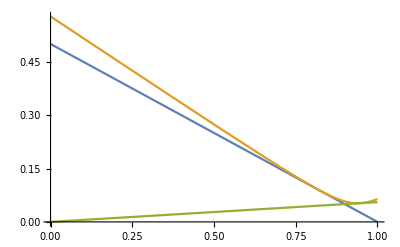

```mathematica
Plot[{ϵ1[z],ϵ2[z],ϵ3[z]},{z,0,1}]
```

```mathematica
"interactive plot"%31DynamicModule[{xc,dx},Manipulate[Plot[{ϵ1[z],ϵ2[z],ϵ3[z]},{z,xc-dx,xc+dx}],{{xc,1/2,"center"},-5/2,7/2},{{dx,0.5,"zoom"},3,0.03}],DynamicModuleValues:>{}]
```

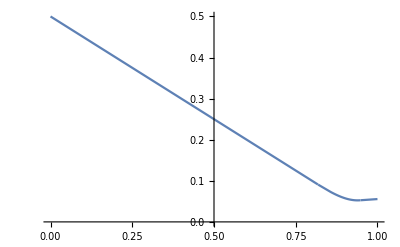

```mathematica
Plot[ϵ4[z],{z,0,1},AxesOrigin->{0.5,0}]
```

```mathematica
"interactive plot"%24DynamicModule[{xc,dx},Manipulate[Plot[ϵ4[z],{z,xc-dx,xc+dx},PlotRange->All,AxesOrigin->{0.5,0}],{{xc,1/2,"center"},-5/2,7/2},{{dx,0.5,"zoom"},3,0.03}],DynamicModuleValues:>{}]
```

```mathematica
ϵ2[171/182]
```

1/(2 √91)